Office dialog

```mathematica
Get["Alex`"];
```

Assured Flow Solutions' Alex v2020.3.30

```mathematica
officeRatings=Import["https://raw.githubusercontent.com/rfordatascience/tidytuesday/master/data/2020/2020-03-17/office_ratings.csv"];
```

```mathematica
officeRatings=officeRatings//associationThreadAll[First[#],Rest[#]]&;
```

```mathematica
officeRatings//Length
```

188

```mathematica
officeRatings[[1]]
```

<|season→1,episode→1,title→Pilot,imdb_rating→7.6,total_votes→3706,air_date→2005-03-24|>

### Quick analysis

```mathematica
smoothOp[data_]:=With[{f=LinearModelFit[data//MapAt[AbsoluteTime,{All,1}],t,t]},
Table[{d[[1]],f[AbsoluteTime[d[[1]]]]},{d,data}]
];
```

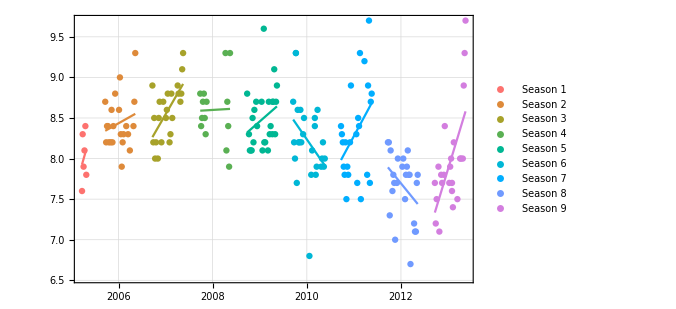

```mathematica
GroupBy[officeRatings,Function[#season]->Function[{#episode,#["air_date"],#["imdb_rating"]}],SortBy[First]/*slice[All,{2,3}]/*MapAt[DateObject,{All,1}]]//KeyMap[ToString/*stringPrepend["Season "]]//Function[Show[
DateListPlot[#,Joined->False,PlotStyle->ggplotColorsFunc[Length[#]],ImageSize->500,GridLines->{Function[{min,max},linearDateGridLines[min,max]],Function[{min,max},linearGridLines[min,max]]},Frame->True,FrameTicks->{{Function[{min,max},linearTicks[min,max]],None},{Automatic,None}},LabelStyle->Directive[12,Black,FontFamily->"Arial"]],
DateListPlot[#//Values//Map[smoothOp],PlotStyle->Thread[{Thick,ggplotColorsFunc[Length[#]]}],Joined->True]
]]
```

### Get office transcript

```mathematica
officeTranscript=Import[FileNameJoin[{NotebookDirectory[],"OfficeTranscript.csv"}]];
```

```mathematica
officeTranscript=officeTranscript//associationThreadAll[First[#],Rest[#]]&;
```

```mathematica
Length[officeTranscript]
```

55130

```mathematica
officeTranscript[[1]]
```

<|index→1,season→1,episode→1,episode_name→Pilot,director→Ken Kwapis,writer→Ricky Gervais;Stephen Merchant;Greg Daniels,character→Michael,text→All right Jim. Your quarterlies look very good. How are things at the library?,text_w_direction→All right Jim. Your quarterlies look very good. How are things at the library?|>

```mathematica
officeTranscript//GroupBy[Function[{#season,#episode,#character}]]//slice[2,1,"text"]
```

Oh, I told you. I couldn't close it. So...

```mathematica
officeTranscript//GroupBy[{Function[#character],Function[#season]->Function[#text]}]//Length
```

769

```mathematica
officeTranscript//GroupBy[{Function[#character],Function[#season]->Function[#text]}]//Select[Total[Length/@#]>1000&]
```

```mathematica
sentiments=officeTranscript//GroupBy[{Function[#character],Function[#season]->Function[#text]}]//Select[Total[Length/@#]>750&]//Map[Map[Function[Check[Classify["Sentiment",#],Nothing]]]];
```

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (30.).

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (200.).

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (250.).

General::stop: Further output of ClassifierFunction::mlincfttp will be suppressed during this calculation.

```mathematica
sentiments=sentiments//Map[Map[Cases["Negative"|"Positive"|"Neutral"]]];
```

```mathematica
sentimentsRanked=Replace[sentiments,{"Negative"->-1,"Positive"->1,"Neutral"->0},{0,Infinity}]//Map[Map[Mean/*N]/*Select[NumericQ]];
```

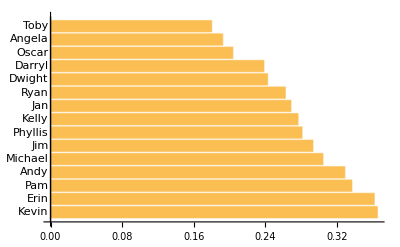

```mathematica
sentimentsRanked//Map[Median]/*ReverseSort//BarChart[#,BarOrigin->Left,ChartLabels->Automatic]&
```